# Cuencas de atracción TFM Víctor Galilea

## José Manuel Gutiérrez Dpto. de Matemáticas y Computación, Universidad de La Rioja, 26004 Logroño, SPAIN

Sigo las notas de Juan Luis [J. L. Varona, Graphic and numerical comparison between iterative methods, Math. Intelligencer 24 (2002), no. 1, 37-46], pasando de los complejos a puntos del plano y eliminando las intensidades de los colores. Para versiones de  Mathematica 6, 7, 8 and 9, se recomienda usar ArrayPlot en vez de DensityPlot.

Ver también CuencasColorgrados4 y 5

## CASO 1 : El método de Newton para z^3 - 1. Versión sencilla (sin intensidad de colores)

#### El método iterativo

```mathematica
p[z_]:=z^3-1;newton[z_]= z-p[z]/p'[z]//Simplify
```

1/(3 z^2)+(2 z)/3

```mathematica
iterNewton = Compile[{{z,_Complex}}, 1/(3 z^2)+(2 z)/3]
```

CompiledFunction[…]

#### Aproximando las raíces

Con esta función asignamos un valor numérico (1, 2 o 3) a cada una de las raíces. Dejamos el 0 para cualquier otra situación.

```mathematica
NSolve[z^3==1,z]
```

{{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ},{z→1.}}

```mathematica
r1=1;r2=-0.5-0.8660254037844386 ⅈ;r3=-0.5+0.8660254037844386 ⅈ;
```

```mathematica
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
```

#### Algoritmos de coloración

```mathematica
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
```

```mathematica
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
```

```mathematica
fractalColorWS[p_] :=
Switch[IntegerPart[p],
3, CMYKColor[1,0.,0.,0],
2, CMYKColor[0.,1,0.,0],
1, CMYKColor[0.,0.,1,0],
0, CMYKColor[0.,0.,0.,1.]
]
```

```mathematica
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
```

```mathematica
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,5},(* Three roots + fixed  *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

#### Variables globales y gráficos

Usar numberPoints = 512 para dibujos con alta precisión

```mathematica
numberPoints =64;
```

```mathematica
limIterations=25;
xxMin=-1.5; xxMax=1.5; yyMin=-1.5; yyMax=1.5;
```

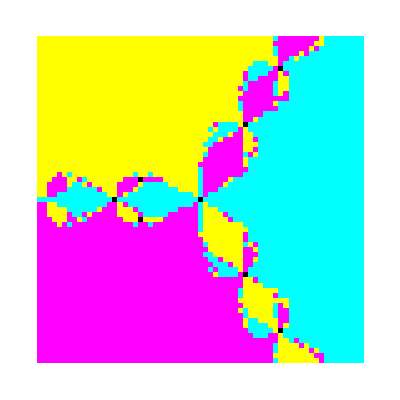

```mathematica
plotColorFractal[iterNewton, numberPoints]
```

## CASO 2 : El método de Newton para z^3 - 1. Versión con intensidad de colores

#### El método iterativo

```mathematica
p[z_]:=z^3-1;newton[z_]= z-p[z]/p'[z]//Simplify
```

1/(3 z^2)+(2 z)/3

```mathematica
iterNewton = Compile[{{z,_Complex}}, 1/(3 z^2)+(2 z)/3]
```

CompiledFunction[…]

#### Aproximando las raíces

Con esta función asignamos un valor numérico (1, 2 o 3) a cada una de las raíces. Dejamos el 0 para cualquier otra situación.

```mathematica
NSolve[z^3==1,z]
```

{{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ},{z→1.}}

```mathematica
r1=1;r2=-0.5-0.8660254037844386 ⅈ;r3=-0.5+0.8660254037844386 ⅈ;
```

```mathematica
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
```

#### Algoritmos de coloración

```mathematica
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
```

```mathematica
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
```

```mathematica
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]]
```

CompiledFunction[…]

```mathematica
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
```

```mathematica
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
```

```mathematica
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

#### Variables globales y gráficos

Usar numberPoints = 512 para dibujos con alta precisión

```mathematica
numberPoints =64;
```

```mathematica
limIterations=25;
xxMin=-1.5; xxMax=1.5; yyMin=-1.5; yyMax=1.5;
```

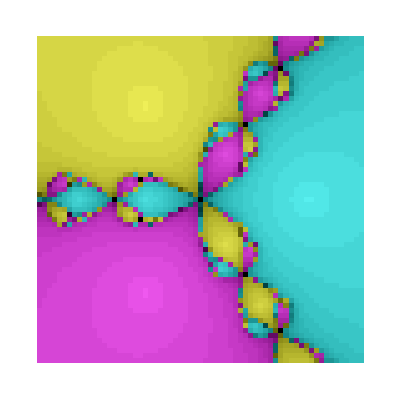

```mathematica
plotColorFractal[iterNewton, numberPoints]
```

## CASO 3 : El método de Schröder para (z^2 - 1)(z-3-I). Versión con intensidad de colores

#### El método iterativo

```mathematica
p[z_]:=(z^2-1)(z-1.5*I);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z]//Simplify//Together
```

((0.5+0. ⅈ) ((0.+1. ⅈ)-(6.+0. ⅈ) z-(0.+10. ⅈ) z^2+(2.66667+0. ⅈ) z^3+(0.+1. ⅈ) z^4))/(-1.16667-(0.+2. ⅈ) z-1.5 z^2-(0.+2. ⅈ) z^3+z^4)

```mathematica
iterSch= Compile[{{z,_Complex}},sp[z]]
```

CompiledFunction[…]

#### Aproximando las raíces

Con esta función asignamos un valor numérico (1, 2 o 3) a cada una de las raíces. Dejamos el 0 para cualquier otra situación.

```mathematica
r1=1;r2=-1;r3=1.5*I;
```

```mathematica
Clear[rootPosition]
```

```mathematica
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
```

#### Algoritmos de coloración

```mathematica
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
```

```mathematica
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
```

```mathematica
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]]
```

CompiledFunction[…]

```mathematica
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,0.]
]
]
```

```mathematica
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
```

```mathematica
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

#### Variables globales y gráficos

Usar numberPoints = 512 para dibujos con alta precisión

```mathematica
numberPoints =32;
```

```mathematica
limIterations=100;
xxMin=-0.00001; xxMax=0.00001; yyMin=10; yyMax=400;
```

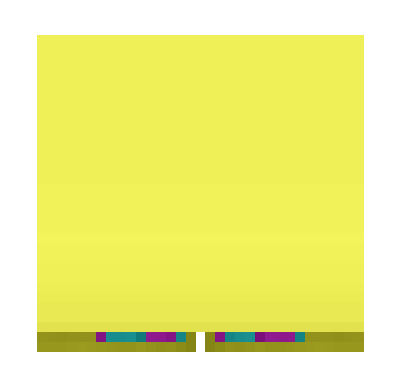

```mathematica
plotColorFractal[iterSch, numberPoints]
```

```mathematica
Lista1=NestList[sp,1.5-4*I,80];
Part[Lista1,73]
Part[Lista1,74]
Part[Lista1,75]
Part[Lista1,76]
```

1.47032-3.1481 ⅈ

0.579967+1.3703 ⅈ

1.47032-3.1481 ⅈ

0.579967+1.3703 ⅈ

```mathematica
a
```

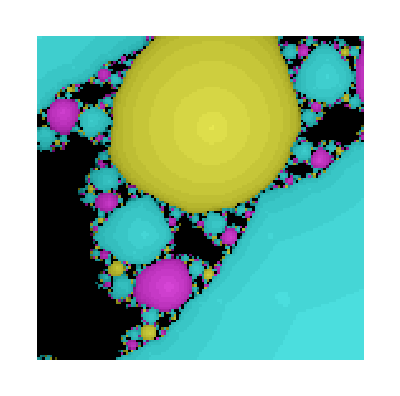

```mathematica
limIterations=25;
xxMin=0; xxMax=0.5; yyMin=0.5; yyMax=1;plotColorFractal[iterSch, numberPoints]
```

Algunos ejemplos

```mathematica
NestList[sp,5.+2I,7]
```

{5.+2. ⅈ,2.30116+0.645591 ⅈ,2.44342+0.669013 ⅈ,2.67241+0.726977 ⅈ,2.91865+0.855273 ⅈ,3.00472+0.979628 ⅈ,3.0003+1.00003 ⅈ,3.+1. ⅈ}

```mathematica
NestList[sp,0.25+0.85I,5]
```

{0.25+0.85 ⅈ,2.94047+1.20797 ⅈ,3.03138+1.00035 ⅈ,2.99938+1.00023 ⅈ,3.+1. ⅈ,3.+1. ⅈ}

Los puntos con Abs[z] grande van a parar al 1 ??

```mathematica
NestList[sp,50.+20.I,7]
```

{50.+20. ⅈ,1.10516+0.347189 ⅈ,0.983518+0.00720964 ⅈ,0.999931-0.0000154578 ⅈ,1.-1.12292×10^-9 ⅈ,1.+1.11022×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ}

En los puntos de la zona negra, parece que hay un 2 - ciclo atractor??

```mathematica
NestList[sp,1.5-4.I,20]
```

{1.5-4. ⅈ,0.611701+1.25582 ⅈ,1.58472-2.52489 ⅈ,0.571496+1.42179 ⅈ,1.37456-3.37352 ⅈ,0.573185+1.33875 ⅈ,1.58172-3.02574 ⅈ,0.589292+1.38748 ⅈ,1.38904-3.19694 ⅈ,0.570969+1.36243 ⅈ,1.52935-3.1375 ⅈ,0.586766+1.37315 ⅈ,1.43432-3.14328 ⅈ,0.575486+1.37006 ⅈ,1.49004-3.1585 ⅈ,0.58262+1.36954 ⅈ,1.46091-3.13818 ⅈ,0.578592+1.37127 ⅈ,1.47371-3.15572 ⅈ,0.580566+1.36946 ⅈ,1.46989-3.143 ⅈ}

```mathematica
NestList[sp,0.6I,20]
```

{0.+0.6 ⅈ,0.372517+1.66514 ⅈ,1.03999-4.21596 ⅈ,0.557402+1.20662 ⅈ,1.98569-2.3625 ⅈ,0.558499+1.46979 ⅈ,1.302-3.56567 ⅈ,0.568526+1.30983 ⅈ,1.67972-2.90006 ⅈ,0.59429+1.40413 ⅈ,1.32992-3.2521 ⅈ,0.564371+1.35408 ⅈ,1.58067-3.11855 ⅈ,0.592238+1.37697 ⅈ,1.40194-3.1462 ⅈ,0.571581+1.36904 ⅈ,1.50933-3.16432 ⅈ,0.585119+1.36935 ⅈ,1.45068-3.13117 ⅈ,0.577199+1.37188 ⅈ,1.47807-3.16186 ⅈ}

Veamos los posibles 2 - ciclos

```mathematica
NSolve[sp[sp[z]]==z, z]
```

{{z→2.27687+2.83279 ⅈ},{z→1.47032-3.1481 ⅈ},{z→3.39654-0.641923 ⅈ},{z→3.+1. ⅈ},{z→-1.19939+1.95366 ⅈ},{z→2.14334+0.624878 ⅈ},{z→1.92894-0.41271 ⅈ},{z→1.2584-1.42498 ⅈ},{z→1.41847+0.938953 ⅈ},{z→-0.552778-1.49267 ⅈ},{z→0.579967+1.3703 ⅈ},{z→0.728858+1.06829 ⅈ},{z→1.},{z→-1.},{z→0.391358-0.731278 ⅈ},{z→0.264219+0.617601 ⅈ},{z→-0.143337+0.0417892 ⅈ}}

Aquí va uno (repulsor)

```mathematica
{sp[2.2768716884441016+2.8327899312870524 ⅈ], sp[3.396535179204767-0.6419232419086757 ⅈ]}
```

{3.39654-0.641923 ⅈ,2.27687+2.83279 ⅈ}

```mathematica
Abs[sp'[2.2768716884441016+2.8327899312870524 ⅈ]* sp'[3.396535179204767-0.6419232419086757 ⅈ]]
```

3.35054

Aquí va otro (atractor)

```mathematica
{sp[1.4703247092017442-3.1480989935926096 ⅈ], sp[0.5799665204399047+1.3702995877138582 ⅈ]}
```

{0.579967+1.3703 ⅈ,1.47032-3.1481 ⅈ}

```mathematica
Abs[sp'[1.4703247092017442-3.1480989935926096 ⅈ]* sp'[0.5799665204399047+1.3702995877138582 ⅈ]]
```

0.612041

Aquí va el tercero (repulsor)

```mathematica
{sp[-1.199386152808877+1.953662561130996 ⅈ], sp[-0.5527776658507195-1.4926720521317551 ⅈ]}
```

{-0.552778-1.49267 ⅈ,-1.19939+1.95366 ⅈ}

```mathematica
Abs[sp'[-1.199386152808877+1.953662561130996 ⅈ]* sp'[-0.5527776658507195-1.4926720521317551 ⅈ]]
```

3.16518

Aquí va el cuarto (repulsor)

```mathematica
{sp[1.928941293268424-0.41271025793147903 ⅈ], sp[0.39135826988711664-0.7312776079974106 ⅈ]}
```

{0.391358-0.731278 ⅈ,1.92894-0.41271 ⅈ}

```mathematica
Abs[sp'[1.928941293268424-0.41271025793147903 ⅈ]* sp'[0.39135826988711664-0.7312776079974106 ⅈ]]
```

11.8606

Aquí va el quinto (repulsor)

```mathematica
{sp[1.2584026712194998-1.4249792436630973 ⅈ], sp[0.7288584752773524+1.0682913455743013 ⅈ]}
```

{0.728858+1.06829 ⅈ,1.2584-1.42498 ⅈ}

```mathematica
Abs[sp'[1.2584026712194998-1.4249792436630973 ⅈ]* sp'[0.7288584752773524+1.0682913455743013 ⅈ]]
```

4.

Y el sexto (repulsor)

```mathematica
{sp[1.4184690580234824+0.9389530543247392 ⅈ], sp[0.2642193928896644+0.6176012233439158 ⅈ]}
```

{0.264219+0.617601 ⅈ,1.41847+0.938953 ⅈ}

```mathematica
Abs[sp'[1.4184690580234824+0.9389530543247392 ⅈ]* sp'[0.2642193928896644+0.6176012233439158 ⅈ]]
```

14.4752

Notemos que sí hay puntos fijos extraños. Son las soluciones de p’[z]=0. En este caso ambos son repulsores.

```mathematica
NSolve[sp[z]==z, z]
```

{{z→3.+1. ⅈ},{z→2.14334+0.624878 ⅈ},{z→-1.},{z→1.},{z→-0.143337+0.0417892 ⅈ}}

```mathematica
NSolve[p'[z]==0, z]
```

{{z→-0.143337+0.0417892 ⅈ},{z→2.14334+0.624878 ⅈ}}

```mathematica
{sp'[-0.14333731987015566+0.0417891603755323 ⅈ], sp'[2.1433373198701555+0.6248775062911344 ⅈ]}
```

{2.-1.66533×10^-16 ⅈ,2.+8.88178×10^-16 ⅈ}